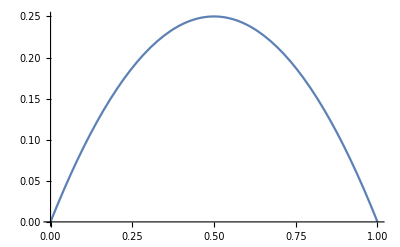

```mathematica
Plot[x(1-x), {x,0, 1}]
```

```mathematica
Maximize[{x(1-x), x≤1, x>0}, x]
```

{1/4,{x→1/2}}

```mathematica
Subscript[c, n]^2(1-Subscript[c, n]^2)/N
```

(c_n^2 (1-c_n^2))/N

```mathematica
%/.{Subscript[c, n]^2 ->x}/.%%[[2]]
```

1/(4 N)

*******************************************************

```mathematica
$Assumptions = n ≤N && n ≥N && n ≥0 && M>0 && M ∈ Integers && n∈Integers && n ≤ M
```

n≤N&&n≥N&&n≥0&&M>0&&M∈ℤ&&n∈ℤ&&n≤M

```mathematica
ψ = Sum[Subscript[c, m]^2, {m,0, M}]^N
```

(∑_(m=0)^M c_m^2)^N

```mathematica
ψ =ψ/.Subscript[c, m]^2->Subscript[C, m]
```

(∑_(m=0)^M C_m)^N

```mathematica
1/N^2 Subscript[C, n] D[Subscript[C, n] D[ψ,Subscript[C, n]], Subscript[C, n]] + (-2/N) Subscript[C, n]^2 D[ψ, Subscript[C, n]] +Subscript[C, n]^2 ψ //Expand
```

C_n^2 (∑_(m=0)^M C_m)^(-2+N)-(C_n^2 (∑_(m=0)^M C_m)^(-2+N))/N+(C_n (∑_(m=0)^M C_m)^(-1+N))/N-2 C_n^2 (∑_(m=0)^M C_m)^(-1+N)+C_n^2 (∑_(m=0)^M C_m)^N

```mathematica
%/.Sum[Subscript[C, m], {m, 0, M}] -> 1
```

C_n/N-C_n^2/N

```mathematica
%/.Subscript[C, n]->Subscript[c, n]^2//Together
```

(c_n^2-c_n^4)/N

*********************************************************************